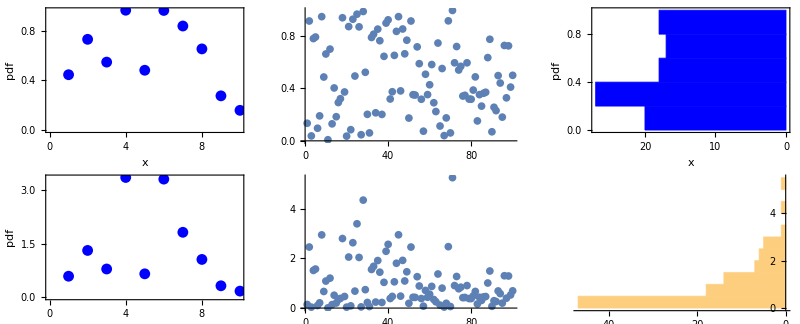

```mathematica
SetDirectory[NotebookDirectory[]];
n=10;
x=RandomReal[{0,1},n];
y=InverseCDF[ExponentialDistribution[1],x];
g1=ListPlot[x,PlotStyle->Blue,PlotRange->Full,Frame->{True,True,False,False},FrameLabel->{"x","pdf"},BaseStyle->{FontSize->18}];
g2=ListPlot[y,PlotStyle->Blue,PlotRange->Full,Frame->{True,True,False,False},FrameLabel->{"x","pdf"},BaseStyle->{FontSize->18}];
n = 100;
x=RandomReal[{0,1},n];
y=InverseCDF[ExponentialDistribution[1],x];
g1a=ListPlot[x];
g2a=ListPlot[y];
g1b = Histogram[x,BarOrigin->Right,ChartStyle->Blue,PlotRange->Full,Frame->{True,True,False,False},FrameLabel->{"x","pdf"},BaseStyle->{FontSize->18}];
g2b = Histogram[y,BarOrigin->Right];
Show[GraphicsGrid[{{g1,g1a,g1b},{g2,g2a,g2b}}],ImageSize->800]
```